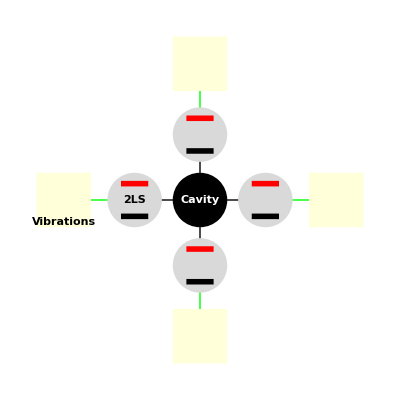
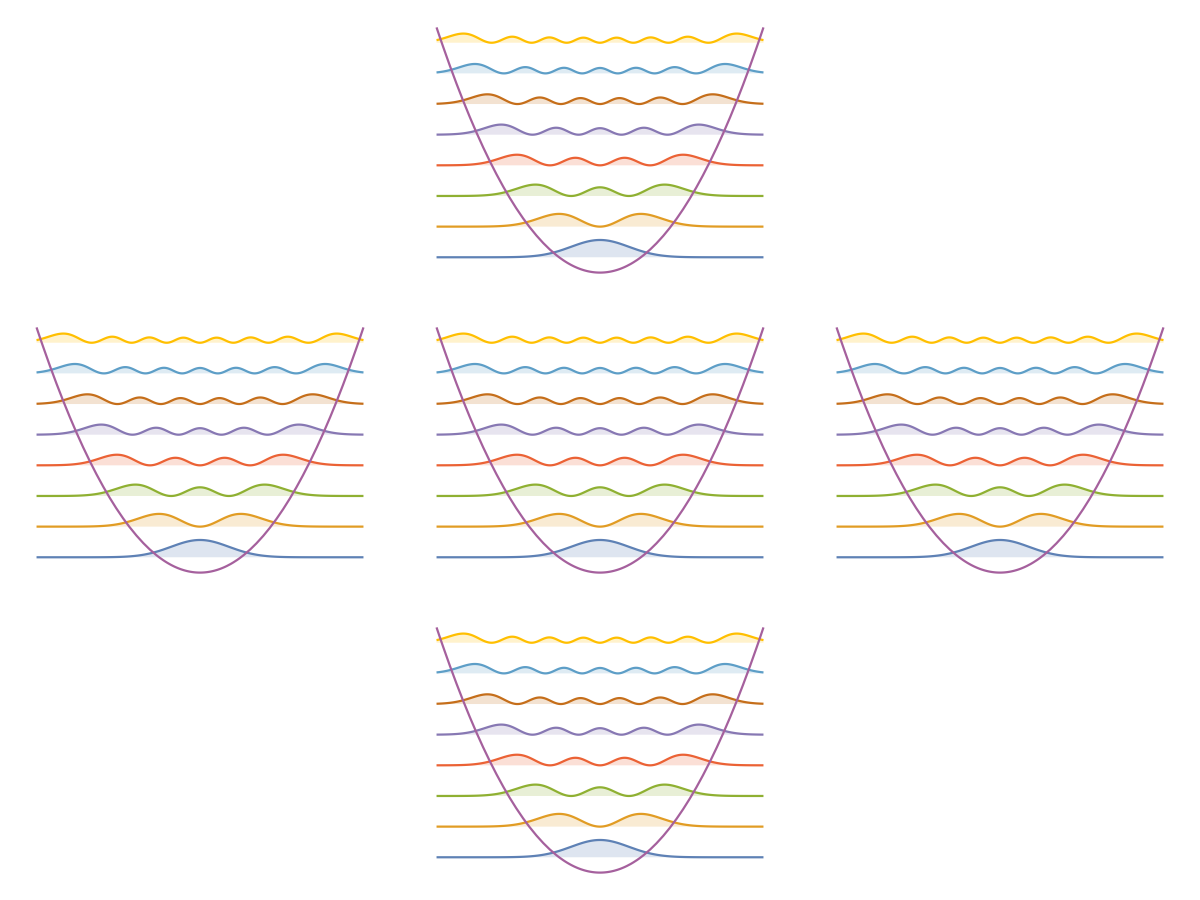

```mathematica
(* Vertices coordinates of a pentagon with first *)

(*{x,y} := {r1 Cos[t+k*2Pi/5],r1 Sin[t+k*2Pi/5]};*)

mkfig[Nmax_]:=Module[{},(*Nmax=6;*)
t=Pi/2; 
X[k_]:=Cos[t+k*2Pi/Nmax];
Y[k_]:=Sin[t+k*2Pi/Nmax];

M=8;
f[n_,x_]:= Abs[((1/Pi)^(1/4)HermiteH[n,x])/(E^(x^2/2)Sqrt[2^n n!])]^2;
pl:=Plot[Evaluate@Append[Table[f[n,x]+n+1/2,{n,0,M-1}],x^2/2]
,{x,-4,4},Filling->Table[n->n-1/2,{n,1,M}],Frame->False,Axes-> False];

Vibmode[r1_,k_,s_]:={Rectangle[{r1 X[k]-s,r1 Y[k]-s},{r1 X[k]+s,r1 Y[k]+s}],
Inset[pl,{r1 X[k],r1 Y[k]},Automatic,2s]
};

TLS[r1_,k_,s_]:={LightGray,Disk[{r1 X[k],r1 Y[k]},s],
Black,Thick,Line[{{r1 X[k]-s/2,r1 Y[k]+iy},{r1 X[k]+s/2,r1 Y[k]+iy}}]/.iy-> -0.6s,
Red,Thick,Line[{{r1 X[k]-s/2,r1 Y[k]+iy},{r1 X[k]+s/2,r1 Y[k]+iy}}]/.iy-> 0.6s};

cx={Black,Thick,Table[Line[{{0,0},{1.2X[i],1.2Y[i]}}],{i,1,Nmax}]};
xp={Green,Thick,  Table[Line[{{1.2X[i],1.2Y[i]},{2.3X[i],2.2 Y[i]}}],{i,1,Nmax}]};
cavity={Black,Thickness[0.01],Disk[{0,0},0.5],Inset[pl,{0,0},Automatic,0.9],Text[Style["Cavity",Bold,White,Thick]]};
exciton={Pink,Thickness[0.01],Table[TLS[1.2,k,0.5],{k,1,Nmax}],
Text[Style["2LS",Bold,Black,Thick],{1.2X[1],1.2Y[1]}]};
phonon={LightYellow,Thick,Table[Vibmode[2.5,k,0.5],{k,1,Nmax}],
Text[Style["Vibrations",Bold,Black,Thick],{2.5X[1],2.5Y[1]-0.4}]};

Graphics[{
cx,xp,
cavity,
exciton,
phonon
}]
];

mkfig[4]
```

```mathematica
Fig[nfilledi_,nfilledf_]:=Module[{label,lab,hopi,hopf,ar2},
x[n_]:= Module[{dd,x,dx},
dx=0.5;dd=0;
If[n>4,dd=0.3]; 
x= Quotient[n,2,1]*dx+dd;
x];
y[n_]:= Module[{y},
y= Mod[n,2,1]*0.3;
y];
dx=0.2;dy=0.15;
l[n_]:=Line[{{x[n]-dx,y[n]},{x[n]+dx,y[n]}}];
ra=Arrow[{{x[3]+1.2dx,y[1]+dy},{x[5]-1.2dx,y[1]+dy}}];
objects=Append[Table[l[n],{n,1,8}],ra];
e[n_]:=Disk[{x[n],y[n]},0.05];
Do[AppendTo[objects,e[n]],{n,nfilledi}];
Do[AppendTo[objects,e[n+4]],{n,nfilledf}];

(* Label hop parameter *)
hopi=Complement[nfilledi,nfilledf][[1]];
hopf=Complement[nfilledf,nfilledi][[1]];
lab="XX";
If[hopi==1&&hopf==3||hopf==1&&hopi==3,lab="t_h"];
If[hopi==2&&hopf==4||hopf==2&&hopi==4,lab="t_l"];
If[hopi==2&&hopf==3||hopf==1&&hopi==4,lab="t_lh"];
If[hopi==1&&hopf==4||hopf==2&&hopi==3,lab="t_hl"];
label=Text[Style[lab,Large,FontFamily->"Arial"],{x[3]+dx+0.15,y[1]+1.5dy}];
AppendTo[objects,label];

If[Abs[hopf-hopi]==2,
y[hopi];
ar2=Arrow[BezierCurve[{{x[hopi],y[hopi]},{(x[hopi]+x[hopf])/2,y[hopi]+dy},{x[hopf],y[hopi]}}]];
,
ar2=Arrow[{{x[hopi],y[hopi]},{x[hopf],y[hopf]}}]
];

AppendTo[objects,ar2];

Graphics[objects,ImageSize->400]
];
```

```mathematica
DhopsR:=(
tab={{Fig[{1,2,4},{2,4,3}],
Fig[{1,2,3},{1,4,3}],
Fig[{1,2,4},{1,4,3}],
Fig[{1,2,3},{2,4,3}]
}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);

DhopsL=(tab={{Fig[{2,3,4},{2,1,4}],
Fig[{1,3,4},{1,2,3}],
Fig[{2,3,4},{1,2,3}],
Fig[{1,3,4},{1,2,4}]}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);


PhihopsR=(tab={{
Fig[{3},{1}],
Fig[{4},{2}],
Fig[{4},{1}],
Fig[{3},{2}]}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);


PhihopsL=(tab={{
Fig[{1},{3}],
Fig[{2},{4}],
Fig[{2},{3}],
Fig[{1},{4}]}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);


DPhiAnnihilation:=(
tab={{Fig[{1,2},{2,3}],
Fig[{1,2},{1,4}],
Fig[{1,2},{1,3}],
Fig[{1,2},{2,4}]
}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);


PhiDAnnihilation:=(
tab={{Fig[{3,4},{1,4}],
Fig[{3,4},{2,3}],
Fig[{3,4},{1,3}],
Fig[{3,4},{2,4}]
}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);



DPhiCreation:=(
tab={{Fig[{2,3},{1,2}],
Fig[{1,4},{1,2}],
Fig[{2,4},{1,2}],
Fig[{1,3},{1,2}]
}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);


PhiDCreation:=(
tab={{Fig[{2,3},{3,4}],
Fig[{1,4},{3,4}],
Fig[{2,4},{3,4}],
Fig[{1,3},{3,4}]
}}//Transpose;
num={Table[
Text[Style["Channel "<>ToString[i],Bold,16]]
,{i,1,4}]}//Transpose;
tab=Join[num,tab,2];
TableForm[tab,TableSpacing->{5,7}]
);


Export[NotebookDirectory[]<>"DhopsR.pdf",DhopsR]
Export[NotebookDirectory[]<>"DhopsL.pdf",DhopsL]
Export[NotebookDirectory[]<>"PhihopsR.pdf",PhihopsR]
Export[NotebookDirectory[]<>"PhihopsL.pdf",PhihopsL]
Export[NotebookDirectory[]<>"DPhiAnnihilation.pdf",DPhiAnnihilation]
Export[NotebookDirectory[]<>"PhiDAnnihilation.pdf",PhiDAnnihilation]
Export[NotebookDirectory[]<>"DPhiCreation.pdf",DPhiCreation]
Export[NotebookDirectory[]<>"PhiDCreation.pdf",PhiDCreation]
```

/Users/panda/repos/transport-code/transport-notes/figs/DhopsR.pdf

/Users/panda/repos/transport-code/transport-notes/figs/DhopsL.pdf

/Users/panda/repos/transport-code/transport-notes/figs/PhihopsR.pdf

/Users/panda/repos/transport-code/transport-notes/figs/PhihopsL.pdf

/Users/panda/repos/transport-code/transport-notes/figs/DPhiAnnihilation.pdf

/Users/panda/repos/transport-code/transport-notes/figs/PhiDAnnihilation.pdf

/Users/panda/repos/transport-code/transport-notes/figs/DPhiCreation.pdf

/Users/panda/repos/transport-code/transport-notes/figs/PhiDCreation.pdf

```mathematica
(*tab={{DhopsR,DhopsL},
{PhihopsR,PhihopsL},
{DPhiAnnihilation,PhiDAnnihilation},
{DPhiCreation,PhiDCreation}};
TableForm[tab,TableSpacing->{1,1}];*)
```